```mathematica
(* Subscript[P, 2] ansatz functions on the standard 2-simplex *)
Subscript[f, 0][u_,v_]:=(1-u-v)*(1-2*u-2*v);
Subscript[f, 1][u_,v_]:=(2*u-1)*u;
Subscript[f, 2][u_,v_]:=(2*v-1)*v;
Subscript[f, 3][u_,v_]:=4*(1-u-v)*u;
Subscript[f, 4][u_,v_]:=4*u*v;
Subscript[f, 5][u_,v_]:=4*(1-u-v)*v;
```

```mathematica
(* Gradients *)
Subscript[df, 0][u_,v_]:=Grad[Subscript[f, 0][u,v],{u,v}];
Subscript[df, 1][u_,v_]:=Grad[Subscript[f, 1][u,v],{u,v}];
Subscript[df, 2][u_,v_]:=Grad[Subscript[f, 2][u,v],{u,v}];
Subscript[df, 3][u_,v_]:=Grad[Subscript[f, 3][u,v],{u,v}];
Subscript[df, 4][u_,v_]:=Grad[Subscript[f, 4][u,v],{u,v}];
Subscript[df, 5][u_,v_]:=Grad[Subscript[f, 5][u,v],{u,v}];
```

```mathematica
(* Function mapping u,v on std. 2-simplex into an arbitrary triangle with vertices Subscript[x, 1],Subscript[x, 2],Subscript[x, 3] *)
(* matrix to obtain (-y,x) from (x,y) *)
J={{0,-1},{1,0}};
g[u_,v_, w_, k_, s_]:=J.(w+(k-w)*u+(s-w)*v);
```

```mathematica
(* Triangle vertices *)
Subscript[x, 1]={0,0};
 Subscript[x, 2]={1,0};
 Subscript[x, 3]={1,1};
 Subscript[x, 4]={0,1};
```

```mathematica
(* jacobians for the transformations *)
Subscript[J, 1]={{0,-1},{1, 0}};
Subscript[J, 2]={{-1,-1},{0,-1}};
Subscript[J, 1,inv]=Inverse[Subscript[J, 1]];
Subscript[J, 2,inv]=Inverse[Subscript[J, 2]];
MatrixForm[Subscript[J, 1,inv]]
MatrixForm[Subscript[J, 2,inv]]
```

(0 | 1
-1 | 0)

(-1 | 1
0 | -1)

```mathematica
(* Contributions to the mass matrix by one triangle are proportional to the integral of appropriate Subscript[P, 2] ansatz functions over the standard 2-simplex *)
```

```mathematica
(* The first vertex *)(*
Subscript[B, 0,0]=Integrate[Subscript[f, 0][x,y]*Subscript[f, 0][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 0,1]=Integrate[Subscript[f, 0][x,y]*Subscript[f, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 0,2]=Integrate[Subscript[f, 0][x,y]*Subscript[f, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 0,3]=Integrate[Subscript[f, 0][x,y]*Subscript[f, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 0,4]=Integrate[Subscript[f, 0][x,y]*Subscript[f, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 0,5]=Integrate[Subscript[f, 0][x,y]*Subscript[f, 5][x,y],{x,0,1},{y,0,1-x}];*)
```

```mathematica
(* The second vertex *)(*
Subscript[B, 1,1]=Integrate[Subscript[f, 1][x,y]*Subscript[f, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 1,2]=Integrate[Subscript[f, 1][x,y]*Subscript[f, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 1,3]=Integrate[Subscript[f, 1][x,y]*Subscript[f, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 1,4]=Integrate[Subscript[f, 1][x,y]*Subscript[f, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 1,5]=Integrate[Subscript[f, 1][x,y]*Subscript[f, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 1,0]= Subscript[B, 0,1];*)
```

```mathematica
(* The third vertex *)(*
Subscript[B, 2,2]=Integrate[Subscript[f, 2][x,y]*Subscript[f, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 2,3]=Integrate[Subscript[f, 2][x,y]*Subscript[f, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 2,4]=Integrate[Subscript[f, 2][x,y]*Subscript[f, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 2,5]=Integrate[Subscript[f, 2][x,y]*Subscript[f, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 2,0]=Subscript[B, 0,2];
Subscript[B, 2,1]= Subscript[B, 1,2];*)
```

```mathematica
(* First midpoint (edge #1) *)(*
Subscript[B, 3,3]=Integrate[Subscript[f, 3][x,y]*Subscript[f, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 3,4]=Integrate[Subscript[f, 3][x,y]*Subscript[f, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 3,5]=Integrate[Subscript[f, 3][x,y]*Subscript[f, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 3,0]=Subscript[B, 0,3];
Subscript[B, 3,1]=Subscript[B, 1,3];
Subscript[B, 3,2]=Subscript[B, 2,3];*)
```

```mathematica
(* Second midpoint (edge #2 ) *)(*
Subscript[B, 4,4]=Integrate[Subscript[f, 4][x,y]*Subscript[f, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 4,5]=Integrate[Subscript[f, 4][x,y]*Subscript[f, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 4,0]=Subscript[B, 0,4];
Subscript[B, 4,1]=Subscript[B, 1,4];
Subscript[B, 4,2]=Subscript[B, 2,4];
Subscript[B, 4,3]=Subscript[B, 3,4];*)
```

```mathematica
(* Third midpoint (edge #3 ) *)(*
Subscript[B, 5,5]=Integrate[Subscript[f, 5][x,y]*Subscript[f, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[B, 5,0]=Subscript[B, 0,5];
Subscript[B, 5,1]=Subscript[B, 1,5];
Subscript[B, 5,2]=Subscript[B, 2,5];
Subscript[B, 5,3]=Subscript[B, 3,5];
Subscript[B, 5,4]=Subscript[B, 4,5];*)
```

```mathematica
B=ParallelTable[Integrate[Subscript[f, i][x,y]*Subscript[f, j][x,y],{x,0,1},{y,0,1-x}],{i,0,5},{j,0,5}];
```

```mathematica
(*Bmat=Table[Subscript[B, i,j],{i,0,5},{j,0,5}];*)
```

```mathematica
(*Bmat//MatrixForm*)
```

```mathematica
(*N[Bmat]//MatrixForm*)
```

```mathematica
(* Contributions to the stiffness matrix by one triangle are proportional to the integral of appropriate gradients of the Subscript[P, 2] ansatz functions over the standard 2-simplex *)
```

```mathematica
(* The first vertex *)(*
Subscript[A, 0,0]=Integrate[Subscript[df, 0][x,y].Subscript[df, 0][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 0,1]=Integrate[Subscript[df, 0][x,y].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 0,2]=Integrate[Subscript[df, 0][x,y].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 0,3]=Integrate[Subscript[df, 0][x,y].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 0,4]=Integrate[Subscript[df, 0][x,y].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 0,5]=Integrate[Subscript[df, 0][x,y].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];*)
```

```mathematica
(* The second vertex *)(*
Subscript[A, 1,1]=Integrate[Subscript[df, 1][x,y].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 1,2]=Integrate[Subscript[df, 1][x,y].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 1,3]=Integrate[Subscript[df, 1][x,y].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 1,4]=Integrate[Subscript[df, 1][x,y].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 1,5]=Integrate[Subscript[df, 1][x,y].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 1,0]= Subscript[A, 0,1];*)
```

```mathematica
(* The third vertex *)(*
Subscript[A, 2,2]=Integrate[Subscript[df, 2][x,y].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 2,3]=Integrate[Subscript[df, 2][x,y].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 2,4]=Integrate[Subscript[df, 2][x,y].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 2,5]=Integrate[Subscript[df, 2][x,y].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 2,0]=Subscript[A, 0,2];
Subscript[A, 2,1]= Subscript[A, 1,2];*)
```

```mathematica
(* First midpoint (edge #1) *)(*
Subscript[A, 3,3]=Integrate[Subscript[df, 3][x,y].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 3,4]=Integrate[Subscript[df, 3][x,y].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 3,5]=Integrate[Subscript[df, 3][x,y].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 3,0]=Subscript[A, 0,3];
Subscript[A, 3,1]=Subscript[A, 1,3];
Subscript[A, 3,2]=Subscript[A, 2,3];*)
```

```mathematica
(* Second midpoint (edge #2 ) *)(*
Subscript[A, 4,4]=Integrate[Subscript[df, 4][x,y].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 4,5]=Integrate[Subscript[df, 4][x,y].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 4,0]=Subscript[A, 0,4];
Subscript[A, 4,1]=Subscript[A, 1,4];
Subscript[A, 4,2]=Subscript[A, 2,4];
Subscript[A, 4,3]=Subscript[A, 3,4];*)
```

```mathematica
(* Third midpoint (edge #3 ) *) (*
Subscript[A, 5,5]=Integrate[Subscript[df, 5][x,y].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[A, 5,0]=Subscript[A, 0,5];
Subscript[A, 5,1]=Subscript[A, 1,5];
Subscript[A, 5,2]=Subscript[A, 2,5];
Subscript[A, 5,3]=Subscript[A, 3,5];
Subscript[A, 5,4]=Subscript[A, 4,5];*)
```

```mathematica
(*Amat=Table[Subscript[A, i,j],{i,0,5},{j,0,5}];*)
```

```mathematica
A1=ParallelTable[Integrate[(Transpose[Subscript[J, 1,inv]].Subscript[df, i][x,y]).(Transpose[Subscript[J, 1,inv]].Subscript[df, j][x,y]),{x,0,1},{y,0,1-x}],{i,0,5},{j,0,5}]
A2=ParallelTable[Integrate[(Transpose[Subscript[J, 2,inv]].Subscript[df, i][x,y]).(Transpose[Subscript[J, 2,inv]].Subscript[df, j][x,y]),{x,0,1},{y,0,1-x}],{i,0,5},{j,0,5}]
```

{{∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx},{∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx,∫_0^1 (1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx},{∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx},{∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx},{∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx},{∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}.Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx}}

{{∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx},{∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx,∫_0^1 (1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx},{∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx},{∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx},{∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4 y,4 x}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4 y,4 x}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4 y,4 x}.Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4 y,4 x}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4 y,4 x}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4 y,4 x}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx},{∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx,∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx}}

```mathematica
(*MatrixForm[Amat]*)
```

```mathematica
(*N[Amat]//MatrixForm*)
```

```mathematica
(* Constructing the full mass matrix *) 
(* Part from Element 1 *)
Mmat1 =SparseArray[{ {1,1}->B_⟦3,3⟧, {1,2}->B_⟦3,1⟧,{1,3}->B_⟦3,2⟧,{1,5}->B_⟦3,4⟧,{1,6}->B_⟦3,5⟧,{1,7}->B_⟦3,6⟧,
{2,2}->B_⟦1,1⟧,{2,3}->B_⟦1,2⟧,{2,5}->B_⟦1,4⟧,{2,6}->B_⟦1,5⟧,{2,7}->B_⟦1,6⟧,
{3,3}->B_⟦2,2⟧,{3,5}->B_⟦2,4⟧, {3,6}->B_⟦2,5⟧,{3,7}->B_⟦2,6⟧, 
{5,5}->B_⟦4,4⟧,{5,6}->B_⟦4,5⟧,{5,7}->B_⟦4,6⟧,
{6,6}->B_⟦5,5⟧,{6,7}->B_⟦5,6⟧,
{7,7}->B_⟦6,6⟧,
{8,8}->0, {9,9}->0}];
(* Part from element 2 *)
Mmat2 =SparseArray[{ {1,1}->B_⟦3,3⟧, {1,3}->B_⟦3,1⟧,{1,4}->B_⟦3,2⟧, {1,6}->B_⟦3,6⟧,{1,8}->B_⟦3,4⟧,{1,9}->B_⟦3,5⟧, 
{3,3}->B_⟦1,1⟧,{3,4}->B_⟦1,2⟧,{3,6}->B_⟦1,6⟧,{3,8}->B_⟦1,4⟧,{3,9}->B_⟦1,5⟧,
{4,4}->B_⟦2,2⟧,{4,6}->B_⟦2,6⟧,{4,8}->B_⟦2,4⟧,{4,9}->B_⟦2,5⟧, 
{6,6}->B_⟦6,6⟧, {6,8}->B_⟦6,4⟧, {6,9}->B_⟦6,5⟧,
{8,8}->B_⟦4,4⟧,{8,9}->B_⟦4,5⟧,
{9,9}->B_⟦5,5⟧}];
Mmat = Mmat1+Transpose[Mmat1]-DiagonalMatrix[Diagonal[Mmat1]]+Mmat2+Transpose[Mmat2]-DiagonalMatrix[Diagonal[Mmat2]];
```

```mathematica
MatrixForm[Mmat1]
MatrixForm[Mmat2]
MatrixForm[Mmat]
```

(1/60 | -1/360 | -1/360 | 0 | -1/90 | 0 | 0 | 0 | 0
0 | 1/60 | -1/360 | 0 | 0 | -1/90 | 0 | 0 | 0
0 | 0 | 1/60 | 0 | 0 | 0 | -1/90 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4/45 | 2/45 | 2/45 | 0 | 0
0 | 0 | 0 | 0 | 0 | 4/45 | 2/45 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4/45 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(1/60 | 0 | -1/360 | -1/360 | 0 | 0 | 0 | -1/90 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/60 | -1/360 | 0 | 0 | 0 | 0 | -1/90
0 | 0 | 0 | 1/60 | 0 | -1/90 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 4/45 | 0 | 2/45 | 2/45
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/45 | 2/45
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/45)

(1/30 | -1/360 | -1/180 | -1/360 | -1/90 | 0 | 0 | -1/90 | 0
-1/360 | 1/60 | -1/360 | 0 | 0 | -1/90 | 0 | 0 | 0
-1/180 | -1/360 | 1/30 | -1/360 | 0 | 0 | -1/90 | 0 | -1/90
-1/360 | 0 | -1/360 | 1/60 | 0 | -1/90 | 0 | 0 | 0
-1/90 | 0 | 0 | 0 | 4/45 | 2/45 | 2/45 | 0 | 0
0 | -1/90 | 0 | -1/90 | 2/45 | 8/45 | 2/45 | 2/45 | 2/45
0 | 0 | -1/90 | 0 | 2/45 | 2/45 | 4/45 | 0 | 0
-1/90 | 0 | 0 | 0 | 0 | 2/45 | 0 | 4/45 | 2/45
0 | 0 | -1/90 | 0 | 0 | 2/45 | 0 | 2/45 | 4/45)

```mathematica
Transpose[Mmat]==Mmat
```

True

```mathematica
(* NOTE! No additional scaling factors (read |det[J]| ) are necessary due to the fact that the triangles are congruent to the standard 2-simplex *)
```

```mathematica
(* Constructing the full stiffness matrix *)
Smat1 =SparseArray[{ {1,1}->A1_⟦3,3⟧, {1,2}->A1_⟦3,1⟧,{1,3}->A1_⟦3,2⟧,{1,5}->A1_⟦3,4⟧,{1,6}->A1_⟦3,5⟧,{1,7}->A1_⟦3,6⟧,
{2,2}->A1_⟦1,1⟧,{2,3}->A1_⟦1,2⟧,{2,5}->A1_⟦1,4⟧,{2,6}->A1_⟦1,5⟧,{2,7}->A1_⟦1,6⟧, 
{3,3}->A1_⟦2,2⟧,{3,5}->A1_⟦2,4⟧, {3,6}->A1_⟦2,5⟧,{3,7}->A1_⟦2,6⟧,
{5,5}->A1_⟦4,4⟧,{5,6}->A1_⟦4,5⟧,{5,7}->A1_⟦4,6⟧,
{6,6}->A1_⟦5,5⟧,{6,7}->A1_⟦5,6⟧,
{7,7}->A1_⟦6,6⟧,
{8,8}->0, {9,9}->0}];
(* Part from element 2 *)
Smat2 =SparseArray[{ {1,1}->A2_⟦3,3⟧, {1,3}->A2_⟦3,1⟧,{1,4}->A2_⟦3,2⟧, {1,6}->A2_⟦3,6⟧,{1,8}->A2_⟦3,4⟧,{1,9}->A2_⟦3,5⟧, 
{3,3}->A2_⟦1,1⟧,{3,4}->A2_⟦1,2⟧,{3,6}->A2_⟦1,6⟧,{3,8}->A2_⟦1,4⟧,{3,9}->A2_⟦1,5⟧,
{4,4}->A2_⟦2,2⟧,{4,6}->A2_⟦2,6⟧,{4,8}->A2_⟦2,4⟧,{4,9}->A2_⟦2,5⟧, 
{6,6}->A2_⟦6,6⟧, {6,8}->A2_⟦6,4⟧, {6,9}->A2_⟦6,5⟧,
{8,8}->A2_⟦4,4⟧,{8,9}->A2_⟦4,5⟧,
{9,9}->A2_⟦5,5⟧}];
Smat = Smat1+Transpose[Smat1]-DiagonalMatrix[Diagonal[Smat1]]+Smat2+Transpose[Smat2]-DiagonalMatrix[Diagonal[Smat2]];
```

```mathematica
MatrixForm[Smat1]
```

(∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
0 | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
0 | 0 | ∫_0^1 (1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
0 | 0 | 0 | 0 | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[Smat2]
```

(∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
0 | 0 | 0 | ∫_0^1 (1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4 y,4 x}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx)

```mathematica
MatrixForm[Smat]
```

(∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 (1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆx+∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 (1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4 y,4 x}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx)

```mathematica
Transpose[Smat]==Smat
```

True

```mathematica
MatrixForm[N[Mmat]]
```

(0.0333333 | -0.00277778 | -0.00555556 | -0.00277778 | -0.0111111 | 0. | 0. | -0.0111111 | 0.
-0.00277778 | 0.0166667 | -0.00277778 | 0. | 0. | -0.0111111 | 0. | 0. | 0.
-0.00555556 | -0.00277778 | 0.0333333 | -0.00277778 | 0. | 0. | -0.0111111 | 0. | -0.0111111
-0.00277778 | 0. | -0.00277778 | 0.0166667 | 0. | -0.0111111 | 0. | 0. | 0.
-0.0111111 | 0. | 0. | 0. | 0.0888889 | 0.0444444 | 0.0444444 | 0. | 0.
0. | -0.0111111 | 0. | -0.0111111 | 0.0444444 | 0.177778 | 0.0444444 | 0.0444444 | 0.0444444
0. | 0. | -0.0111111 | 0. | 0.0444444 | 0.0444444 | 0.0888889 | 0. | 0.
-0.0111111 | 0. | 0. | 0. | 0. | 0.0444444 | 0. | 0.0888889 | 0.0444444
0. | 0. | -0.0111111 | 0. | 0. | 0.0444444 | 0. | 0.0444444 | 0.0888889)

```mathematica
MatrixForm[N[Smat]]
```

NIntegrate::inumr: The integrand Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{0,-1+4 y} has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{0,-1+4 y} has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

(NIntegrate[Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{0,-1+4 y},{x,0,1},{y,0,1-x}]+NIntegrate[Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{0,-1+4 y},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y},{x,0,1},{y,0,1-x}]+NIntegrate[Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}]+NIntegrate[Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
NIntegrate[Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | 0.
NIntegrate[Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y},{x,0,1},{y,0,1-x}]+NIntegrate[Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | NIntegrate[(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1}]+NIntegrate[Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}]+NIntegrate[Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
NIntegrate[Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | NIntegrate[(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1}] | 0. | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
NIntegrate[Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | 0.
NIntegrate[Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}]+NIntegrate[Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}]+NIntegrate[Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}]+NIntegrate[Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
NIntegrate[Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | 0.
NIntegrate[Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
NIntegrate[Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[Transpose[(-1 | 1
0 | -1)].{4 y,4 x}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}])

```mathematica
(* Computation of the damping matrix *)
```

```mathematica
(* The first vertex *)
Subscript[C1, 0,0]=Integrate[Subscript[f, 0][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 0][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 0,1]=Integrate[Subscript[f, 0][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 0,2]=Integrate[Subscript[f, 0][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 0,3]=Integrate[Subscript[f, 0][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 0,4]=Integrate[Subscript[f, 0][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 0,5]=Integrate[Subscript[f, 0][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
```

```mathematica
(* The second vertex *)
Subscript[C1, 1,1]=Integrate[Subscript[f, 1][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 1,2]=Integrate[Subscript[f, 1][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 1,3]=Integrate[Subscript[f, 1][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 1,4]=Integrate[Subscript[f, 1][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 1,5]=Integrate[Subscript[f, 1][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 1,0]= Integrate[Subscript[f, 1][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 0][x,y],{x,0,1},{y,0,1-x}];
```

```mathematica
(* The third vertex *)
Subscript[C1, 2,2]=Integrate[Subscript[f, 2][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 2,3]=Integrate[Subscript[f, 2][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 2,4]=Integrate[Subscript[f, 2][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 2,5]=Integrate[Subscript[f, 2][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 2,0]=Integrate[Subscript[f, 2][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 0][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 2,1]= Integrate[Subscript[f, 2][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
```

```mathematica
(* First midpoint (edge #1) *)
Subscript[C1, 3,3]=Integrate[Subscript[f, 3][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 3,4]=Integrate[Subscript[f, 3][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 3,5]=Integrate[Subscript[f, 3][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 3,0]=Integrate[Subscript[f, 3][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 0][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 3,1]=Integrate[Subscript[f, 3][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 3,2]=Integrate[Subscript[f, 3][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
```

```mathematica
(* Second midpoint (edge #2 ) *)
Subscript[C1, 4,4]=Integrate[Subscript[f, 4][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 4,5]=Integrate[Subscript[f, 4][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 4,0]=Integrate[Subscript[f, 4][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 0][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 4,1]=Integrate[Subscript[f, 4][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 4,2]=Integrate[Subscript[f, 4][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 4,3]=Integrate[Subscript[f, 4][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
```

```mathematica
(* Third midpoint (edge #3 ) *)
Subscript[C1, 5,5]=Integrate[Subscript[f, 5][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 5,0]=Integrate[Subscript[f, 5][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 0][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 5,1]=Integrate[Subscript[f, 5][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 5,2]=Integrate[Subscript[f, 5][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 5,3]=Integrate[Subscript[f, 5][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[C1, 5,4]=Integrate[Subscript[f, 5][x,y]*(g[x,y, Subscript[x, 2],Subscript[x, 3], Subscript[x, 1]]).Transpose[Subscript[J, 1,inv]].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
```

```mathematica
(* ELEMENT 2 *)
```

```mathematica
(* The first vertex *)
Subscript[C2, 0,0]=Integrate[Subscript[f, 0][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 0][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 0,1]=Integrate[Subscript[f, 0][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 0,2]=Integrate[Subscript[f, 0][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 0,3]=Integrate[Subscript[f, 0][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 0,4]=Integrate[Subscript[f, 0][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 0,5]=Integrate[Subscript[f, 0][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
```

```mathematica
(* The second vertex *)
Subscript[C2, 1,1]=Integrate[Subscript[f, 1][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 1,2]=Integrate[Subscript[f, 1][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 1,3]=Integrate[Subscript[f, 1][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 1,4]=Integrate[Subscript[f, 1][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 1,5]=Integrate[Subscript[f, 1][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 1,0]= Integrate[Subscript[f, 1][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 0][x,y],{x,0,1},{y,0,1-x}];
```

```mathematica
(* The third vertex *)
Subscript[C2, 2,2]=Integrate[Subscript[f, 2][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 2,3]=Integrate[Subscript[f, 2][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 2,4]=Integrate[Subscript[f, 2][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 2,5]=Integrate[Subscript[f, 2][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 2,0]=Integrate[Subscript[f, 2][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 0][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 2,1]= Integrate[Subscript[f, 2][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
```

```mathematica
(* First midpoint (edge #1) *)
Subscript[C2, 3,3]=Integrate[Subscript[f, 3][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 3,4]=Integrate[Subscript[f, 3][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 3,5]=Integrate[Subscript[f, 3][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 3,0]=Integrate[Subscript[f, 3][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 0][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 3,1]=Integrate[Subscript[f, 3][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 3,2]=Integrate[Subscript[f, 3][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
```

```mathematica
(* Second midpoint (edge #2 ) *)
Subscript[C2, 4,4]=Integrate[Subscript[f, 4][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 4,5]=Integrate[Subscript[f, 4][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 4,0]=Integrate[Subscript[f, 4][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 0][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 4,1]=Integrate[Subscript[f, 4][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 4,2]=Integrate[Subscript[f, 4][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 4,3]=Integrate[Subscript[f, 4][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
```

```mathematica
(* Third midpoint (edge #3 ) *)
Subscript[C2, 5,5]=Integrate[Subscript[f, 5][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 5][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 5,0]=Integrate[Subscript[f, 5][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 0][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 5,1]=Integrate[Subscript[f, 5][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 1][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 5,2]=Integrate[Subscript[f, 5][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 2][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 5,3]=Integrate[Subscript[f, 5][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 3][x,y],{x,0,1},{y,0,1-x}];
Subscript[C2, 5,4]=Integrate[Subscript[f, 5][x,y]*(g[x,y, Subscript[x, 3],Subscript[x, 4], Subscript[x, 1]]).Transpose[Subscript[J, 2,inv]].Subscript[df, 4][x,y],{x,0,1},{y,0,1-x}];
```

```mathematica
(* We have to anti-symmetrize by hand because the local nodal functions have no idea of the global structure of the vector field. *)
```

```mathematica
Cmat1 =SparseArray[{ {1,1}->0, {1,2}->Subscript[C1, 2,0],{1,3}->Subscript[C1, 2,1],{1,5}->Subscript[C1, 2,3],{1,6}->Subscript[C1, 2,4],{1,7}->Subscript[C1, 2,5],{2,1}->-1*Subscript[C1, 2,0],{3,1}->-1*Subscript[C1, 2,1],{5,1}->-1*Subscript[C1, 2,3],{6,1}->-1*Subscript[C1, 2,4],{7,1}->-1*Subscript[C1, 2,5],
{2,2}->0,{2,3}->Subscript[C1, 0,1],{2,5}->Subscript[C1, 0,3],{2,6}->Subscript[C1, 0,4],{2,7}->Subscript[C1, 0,5], {3,2}->-1*Subscript[C1, 0,1],{5,2}->-1*Subscript[C1, 0,3],{6,2}->-1*Subscript[C1, 0,4],{7,2}->-1*Subscript[C1, 0,5],
{3,3}->0,{3,5}->Subscript[C1, 1,3], {3,6}->Subscript[C1, 1,4],{3,7}->Subscript[C1, 1,5], {5,3}->-1*Subscript[C1, 1,3],{6,3}->-1*Subscript[C1, 1,4],{7,3}->-1*Subscript[C1, 1,5],
{5,5}->0,{5,6}->Subscript[C1, 3,4],{5,7}->Subscript[C1, 3,5],{6,5}->-1*Subscript[C1, 3,4],{7,5}->-1*Subscript[C1, 3,5],
{6,6}->0,{6,7}->Subscript[C1, 4,5],{7,6}->-1*Subscript[C1, 4,5],
{7,7}->0,
{8,8}->0, {9,9}->0}];
(* Part from element 2 *)
Cmat2 =SparseArray[{ {1,1}->0, {1,3}->Subscript[C2, 2,0],{1,4}->Subscript[C2, 2,1], {1,6}->Subscript[C2, 2,5],{1,8}->Subscript[C2, 2,3],{1,9}->Subscript[C2, 2,4],  {3,1}->-1*Subscript[C2, 2,0],{4,1}->-1*Subscript[C2, 2,1], {6,1}->-1*Subscript[C2, 2,5],{8,1}->-1*Subscript[C2, 2,3],{9,1}->-1*Subscript[C2, 2,4],
{3,3}->0,{3,4}->Subscript[C2, 0,1],{3,6}->Subscript[C2, 0,5],{3,8}->Subscript[C2, 0,3],{3,9}->Subscript[C2, 0,4],{4,3}->-1*Subscript[C2, 0,1],{6,3}->-1*Subscript[C2, 0,5],{8,3}->-1*Subscript[C2, 0,3],{9,3}->-1*Subscript[C2, 0,4],
{4,4}->0,{4,6}->Subscript[C2, 1,5],{4,8}->Subscript[C2, 1,3],{4,9}->Subscript[C2, 1,4], {6,4}->-1*Subscript[C2, 1,5],{8,4}->-1*Subscript[C2, 1,3],{9,4}->-1*Subscript[C2, 1,4],
{6,6}->0, {6,8}->Subscript[C2, 5,3],{6,9}->Subscript[C2, 5,4],{8,6}->-1*Subscript[C2, 5,3], {9,6}->-1*Subscript[C2, 5,4],
{8,8}->0,{8,9}->Subscript[C2, 3,4],{9,8}->-1*Subscript[C2, 3,4],
{9,9}->0}];

Cmat = Normal[Cmat1]-Diagonal[Normal[Cmat1]]+Normal[Cmat2]-Diagonal[Normal[Cmat2]];
```

```mathematica
MatrixForm[Cmat]
```

(0 | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx+∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx+∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx+∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | 0 | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | 0 | 0 | -4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | -4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx-∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | 4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) x y {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | -4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | -4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | -4 ∫_0^1 ∫_0^(1-x) x y {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0 | 0
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | 0 | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | 0 | 0 | -4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0)

```mathematica
Transpose[Cmat]==-1*Cmat
```

True

```mathematica
MatrixForm[N[Cmat]]
```

NIntegrate::inumr: The integrand y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y} has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0} has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

(0. | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}]+NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}]+NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | 0.
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}]-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}]+NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | 0. | NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | 0. | 0. | -4. NIntegrate[x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | -4. NIntegrate[x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | 0.
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}]-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}]-1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | 4. NIntegrate[x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[x y {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | -4. NIntegrate[y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | -4. NIntegrate[y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | -4. NIntegrate[x y {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | 0. | 0.
-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | 0. | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | 0. | 0. | -4. NIntegrate[x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0.)

```mathematica
Transpose[Cmat1]==-1*Cmat1
```

True

```mathematica
MatrixForm[Cmat2]
```

(0 | 0 | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | 0 | 0 | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | 0 | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | 0 | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | 0 | 0 | 0 | -4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | -4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | 0 | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | 0 | 0 | -4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0)

```mathematica
Transpose[Cmat2]==Cmat2
```

SparseArray[<30>, {9, 9}]==SparseArray[<30>, {9, 9}]

Triangle[{{1,0},{1,1},{0,0}}]

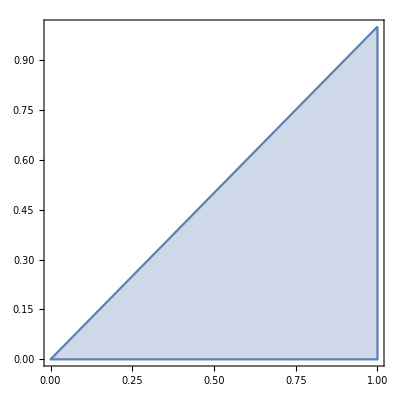

```mathematica
T=Triangle[{Subscript[x, 2],Subscript[x, 3],Subscript[x, 1]}]
RegionPlot[T]
```

Triangle[{{1,1},{0,1},{0,0}}]

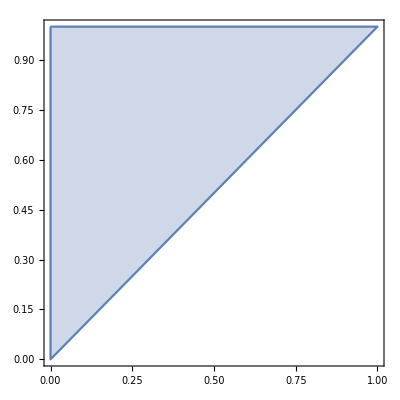

```mathematica
T2=Triangle[{Subscript[x, 3],Subscript[x, 4],Subscript[x, 1]}]
RegionPlot[T2]
```

```mathematica
MatrixForm[Cmat1+Cmat2]
```

(0 | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx+∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx+∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx+∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | 0 | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | 0 | 0 | -4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | -4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx-∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | 4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) x y {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | -4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | -4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | -4 ∫_0^1 ∫_0^(1-x) x y {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0 | 0
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | 0 | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | 0 | 0 | -4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0)

```mathematica
MatrixForm[Mmat]
Dimensions[Mmat]
```

(1/30 | -1/360 | -1/180 | -1/360 | -1/90 | 0 | 0 | -1/90 | 0
-1/360 | 1/60 | -1/360 | 0 | 0 | -1/90 | 0 | 0 | 0
-1/180 | -1/360 | 1/30 | -1/360 | 0 | 0 | -1/90 | 0 | -1/90
-1/360 | 0 | -1/360 | 1/60 | 0 | -1/90 | 0 | 0 | 0
-1/90 | 0 | 0 | 0 | 4/45 | 2/45 | 2/45 | 0 | 0
0 | -1/90 | 0 | -1/90 | 2/45 | 8/45 | 2/45 | 2/45 | 2/45
0 | 0 | -1/90 | 0 | 2/45 | 2/45 | 4/45 | 0 | 0
-1/90 | 0 | 0 | 0 | 0 | 2/45 | 0 | 4/45 | 2/45
0 | 0 | -1/90 | 0 | 0 | 2/45 | 0 | 2/45 | 4/45)

{9,9}

```mathematica
MatrixForm[Smat]
```

(∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 (1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆx+∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 (1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx+∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{0,-1+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{4 y,4 x}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{0,-1+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-3+4 x+4 y,-3+4 x+4 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) Transpose[(-1 | 1
0 | -1)].{4 y,4 x}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx)

```mathematica
MatrixForm[Cmat]
```

(0 | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx+∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx+∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx+∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0}ⅆyⅆx | 0 | 0 | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | 0 | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | ∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | 0 | 0 | -4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | -4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx-∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | 4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) x y {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | -4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | -4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | -4 ∫_0^1 ∫_0^(1-x) x y {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y}ⅆyⅆx | 0 | 0 | 0
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | 0 | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x}ⅆyⅆx | 0 | 0 | -4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx
-∫_0^1 ∫_0^(1-x) y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | -∫_0^1 ∫_0^(1-x) (-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | -∫_0^1 ∫_0^(1-x) x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0 | 4 ∫_0^1 ∫_0^(1-x) x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x}ⅆyⅆx | 0)

```mathematica
MatrixForm[N[Mmat]]
```

(0.0333333 | -0.00277778 | -0.00555556 | -0.00277778 | -0.0111111 | 0. | 0. | -0.0111111 | 0.
-0.00277778 | 0.0166667 | -0.00277778 | 0. | 0. | -0.0111111 | 0. | 0. | 0.
-0.00555556 | -0.00277778 | 0.0333333 | -0.00277778 | 0. | 0. | -0.0111111 | 0. | -0.0111111
-0.00277778 | 0. | -0.00277778 | 0.0166667 | 0. | -0.0111111 | 0. | 0. | 0.
-0.0111111 | 0. | 0. | 0. | 0.0888889 | 0.0444444 | 0.0444444 | 0. | 0.
0. | -0.0111111 | 0. | -0.0111111 | 0.0444444 | 0.177778 | 0.0444444 | 0.0444444 | 0.0444444
0. | 0. | -0.0111111 | 0. | 0.0444444 | 0.0444444 | 0.0888889 | 0. | 0.
-0.0111111 | 0. | 0. | 0. | 0. | 0.0444444 | 0. | 0.0888889 | 0.0444444
0. | 0. | -0.0111111 | 0. | 0. | 0.0444444 | 0. | 0.0444444 | 0.0888889)

```mathematica
MatrixForm[N[Cmat]]
```

NIntegrate::inumr: The integrand y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y} has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0} has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

(0. | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}]+NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}]+NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | 0.
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}]-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}]+NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | 0. | NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | 0. | 0. | -4. NIntegrate[x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | -4. NIntegrate[x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | 0.
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}]-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}]-1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | 4. NIntegrate[x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[x y {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | -4. NIntegrate[y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | -4. NIntegrate[y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | -4. NIntegrate[x y {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | 0. | 0.
-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | 0. | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | 0. | 0. | -4. NIntegrate[x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0.)

```mathematica
MatrixForm[N[Cmat1+Cmat2]]
```

NIntegrate::inumr: The integrand y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0} has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y} has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

(0. | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}]+NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}]+NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | 0.
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}]-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+2 x-2 (1-x-y)+2 y,-1+2 x-2 (1-x-y)+2 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}]+NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-1+4 x,0},{x,0,1},{y,0,1-x}] | 0. | 0. | NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | 0. | NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | 0. | 0. | -4. NIntegrate[x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | -4. NIntegrate[x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | 0.
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}]-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}]-1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | 4. NIntegrate[x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[x y {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | -4. NIntegrate[y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | -4. NIntegrate[y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4 (1-x-y)-4 y},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[x (-1+x+y) {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | -4. NIntegrate[x y {-x,1-y}.Transpose[(0 | 1
-1 | 0)].{-4 y,4-4 x-8 y},{x,0,1},{y,0,1-x}] | 0. | 0. | 0.
-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | 0. | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{-4 x+4 (1-x-y),-4 x},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4-8 x-4 y,-4 x},{x,0,1},{y,0,1-x}] | 0. | 0. | -4. NIntegrate[x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}]
-1. NIntegrate[y (-1+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | -1. NIntegrate[(-1+x+y) (-1+2 x+2 y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | -1. NIntegrate[x (-1+2 x) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[y (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0. | 4. NIntegrate[x (-1+x+y) {-1+y,1-x-y}.Transpose[(-1 | 1
0 | -1)].{4 y,4 x},{x,0,1},{y,0,1-x}] | 0.)

```mathematica
(* Mass matrix for Subscript[P, 2] elements on a refined mesh *)
(* Element #1 *)
Subscript[M, 1]=SparseArray[{ {5,5}->B_⟦1,1⟧,{5,6}->B_⟦1,2⟧,{5,7}->B_⟦1,3⟧,{5,10}->B_⟦1,4⟧,{5,11}->B_⟦1,5⟧,{5,12}->B_⟦1,6⟧,
{6,6}->B_⟦2,2⟧,{6,7}->B_⟦2,3⟧,{6,10}->B_⟦2,4⟧,{6,11}->B_⟦2,5⟧,{6,12}->B_⟦2,6⟧,
{7,7}->B_⟦3,3⟧,{7,10}->B_⟦3,4⟧,{7,11}->B_⟦3,5⟧,{7,12}->B_⟦3,6⟧,
{10,10}->B_⟦4,4⟧,{10,11}->B_⟦4,5⟧,{10,12}->B_⟦4,6⟧,
{11,11}->B_⟦5,5⟧,{11,12}->B_⟦5,6⟧,
{12,12}->B_⟦6,6⟧,
{24,25}->0, {25,25}->0}]; (* ok *)
(* Element #2 *)
Subscript[M, 2]=SparseArray[{{6,6}->B_⟦3,3⟧,{6,8}->B_⟦3,1⟧,{6,9}->B_⟦3,2⟧,{6,13}->B_⟦3,4⟧,{6,14}->B_⟦3,5⟧,{6,15}->B_⟦3,6⟧,
{8,8}->B_⟦1,1⟧,{8,9}->B_⟦1,2⟧,{8,13}->B_⟦1,4⟧,{8,14}->B_⟦1,5⟧,{8,15}->B_⟦1,6⟧,
{9,9}->B_⟦2,2⟧,{9,13}->B_⟦2,4⟧,{9,14}->B_⟦2,5⟧,{9,15}->B_⟦2,6⟧,
{13,13}->B_⟦4,4⟧,{13,14}->B_⟦4,5⟧,{13,15}->B_⟦4,6⟧,
{14,14}->B_⟦5,5⟧,{14,15}->B_⟦5,6⟧,
{15,15}->B_⟦6,6⟧,
{24,25}->0, {25,25}->0}]; (* OK *)
(* Element #3 *)
Subscript[M, 3]=SparseArray[{ {2,2}->B_⟦1,1⟧,{2,5}->B_⟦1,2⟧,{2,7}->B_⟦1,3⟧,{2,12}->B_⟦1,5⟧,{2,16}->B_⟦1,4⟧,{2,17}->B_⟦1,6⟧,
{5,5}->B_⟦2,2⟧,{5,7}->B_⟦2,3⟧,{5,12}->B_⟦2,5⟧,{5,16}->B_⟦2,4⟧,{5,17}->B_⟦2,6⟧,
{7,7}->B_⟦3,3⟧,{7,12}->B_⟦3,5⟧,{7,16}->B_⟦3,4⟧,{7,17}->B_⟦3,6⟧,
{12,12}->B_⟦5,5⟧,{12,16}->B_⟦5,4⟧,{12,17}->B_⟦5,6⟧,
{16,16}->B_⟦4,4⟧,{16,17}->B_⟦4,6⟧,
{17,17}->B_⟦6,6⟧,{24,25}->0, {25,25}->0}];
(* Element #4 *)
Subscript[M, 4]=SparseArray[{ {3,3}->B_⟦2,2⟧,{3,5}->B_⟦2,1⟧,{3,6}->B_⟦2,3⟧,{3,10}->B_⟦2,6⟧,{3,18}->B_⟦2,4⟧,{3,19}->B_⟦2,5⟧,
{5,5}->B_⟦1,1⟧,{5,6}->B_⟦1,3⟧,{5,10}->B_⟦1,6⟧,{5,18}->B_⟦1,4⟧,{5,19}->B_⟦1,5⟧,
{6,6}->B_⟦3,3⟧,{6,10}->B_⟦3,6⟧,{6,18}->B_⟦3,4⟧,{6,19}->B_⟦3,5⟧,
{10,10}->B_⟦6,6⟧,{10,18}->B_⟦6,4⟧,{10,19}->B_⟦6,5⟧,
{18,18}->B_⟦4,4⟧,{18,19}->B_⟦4,5⟧,
{19,19}->B_⟦5,5⟧,
{24,25}->0, {25,25}->0}];
(* Element #5 *)
Subscript[M, 5]=SparseArray[{ {1,1}->B_⟦2,2⟧,{1,6}->B_⟦2,1⟧,{1,7}->B_⟦2,3⟧,{1,11}->B_⟦2,6⟧,{1,20}->B_⟦2,4⟧,{1,21}->B_⟦2,5⟧,
{6,6}->B_⟦1,1⟧,{6,7}->B_⟦1,3⟧,{6,11}->B_⟦1,6⟧,{6,20}->B_⟦1,4⟧,{6,21}->B_⟦1,5⟧,
{7,7}->B_⟦3,3⟧,{7,11}->B_⟦3,6⟧,{7,20}->B_⟦3,4⟧,{7,21}->B_⟦3,5⟧,
{11,11}->B_⟦6,6⟧,{11,20}->B_⟦6,4⟧,{11,21}->B_⟦6,5⟧,
{20,20}->B_⟦4,4⟧,{20,21}->B_⟦4,5⟧,
{21,21}->B_⟦5,5⟧,
{24,25}->0, {25,25}->0}];
(* Element #6 *)
Subscript[M, 6]=SparseArray[{ {3,3}->B_⟦1,1⟧,{3,6}->B_⟦1,3⟧,{3,8}->B_⟦1,2⟧,{3,15}->B_⟦1,5⟧,{3,19}->B_⟦1,6⟧,{3,22}->B_⟦1,4⟧,
{6,6}->B_⟦3,3⟧,{6,8}->B_⟦3,2⟧,{6,15}->B_⟦3,5⟧,{6,19}->B_⟦3,6⟧,{6,22}->B_⟦3,4⟧,
{8,8}->B_⟦2,2⟧,{8,15}->B_⟦2,5⟧,{8,19}->B_⟦2,6⟧,{8,22}->B_⟦2,4⟧,
{15,15}->B_⟦5,5⟧,{15,19}->B_⟦5,6⟧,{15,22}->B_⟦5,4⟧,
{19,19}->B_⟦6,6⟧,{19,22}->B_⟦6,4⟧,
{22,22}->B_⟦4,4⟧,
{24,25}->0, {25,25}->0}];
(* Element #7 *)
Subscript[M, 7]=SparseArray[{ {4,4}->B_⟦2,2⟧,{4,8}->B_⟦2,1⟧,{4,9}->B_⟦2,3⟧,{4,13}->B_⟦2,6⟧,{4,23}->B_⟦2,4⟧,{4,24}->B_⟦2,5⟧,
{8,8}->B_⟦1,1⟧,{8,9}->B_⟦1,3⟧,{8,13}->B_⟦1,6⟧,{8,23}->B_⟦1,4⟧,{8,24}->B_⟦1,5⟧,
{9,9}->B_⟦3,3⟧,{9,13}->B_⟦3,6⟧,{9,23}->B_⟦3,4⟧,{9,24}->B_⟦3,5⟧,
{13,13}->B_⟦6,6⟧,{13,23}->B_⟦6,4⟧,{13,24}->B_⟦6,5⟧,
{23,23}->B_⟦4,4⟧,{23,24}->B_⟦4,5⟧,
{24,24}->B_⟦5,5⟧,{25,24}->0,{25,25}->0}];
(* Element #8 *)
Subscript[M, 8]=SparseArray[{ {1,1}->B_⟦3,3⟧,{1,6}->B_⟦3,2⟧,{1,9}->B_⟦3,1⟧,{1,14}->B_⟦3,4⟧,{1,20}->B_⟦3,5⟧,{1,25}->B_⟦3,6⟧,
{6,6}->B_⟦2,2⟧,{6,9}->B_⟦2,1⟧,{6,14}->B_⟦2,4⟧,{6,20}->B_⟦2,5⟧,{6,25}->B_⟦2,6⟧,
{9,9}->B_⟦1,1⟧,{9,14}->B_⟦1,4⟧,{9,20}->B_⟦1,5⟧,{9,25}->B_⟦1,6⟧,
{14,14}->B_⟦4,4⟧,{14,20}->B_⟦4,5⟧,{14,25}->B_⟦4,6⟧,
{20,20}->B_⟦5,5⟧,{20,25}->B_⟦5,6⟧,
{25,25}->B_⟦6,6⟧}];
```

```mathematica
(* scale the entries by |det J| because each triangle is now only 1/4 the size of the std-simplex *)
For[i=1,i≤8,i++, Subscript[M, i]*=1/4;];
(* create the mass matrix *)
MassMatrixRef = Sum[Subscript[M, i]+Transpose[Subscript[M, i]]-DiagonalMatrix[Diagonal[Subscript[M, i]]],{i,1,8}];
```

```mathematica
MatrixForm[MassMatrixRef]
```

(1/120 | 0 | 0 | 0 | 0 | -1/720 | -1/1440 | 0 | -1/1440 | 0 | -1/360 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/240 | 0 | 0 | -1/1440 | 0 | -1/1440 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/120 | 0 | -1/1440 | -1/720 | 0 | -1/1440 | 0 | -1/360 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/240 | 0 | 0 | 0 | -1/1440 | -1/1440 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/1440 | -1/1440 | 0 | 1/80 | -1/720 | -1/720 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 0 | -1/360 | 0 | -1/360 | 0 | 0 | 0 | 0 | 0 | 0
-1/720 | 0 | -1/720 | 0 | -1/720 | 1/40 | -1/720 | -1/720 | -1/720 | 0 | 0 | -1/360 | -1/360 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | -1/360 | -1/360 | 0 | 0 | -1/360
-1/1440 | -1/1440 | 0 | 0 | -1/720 | -1/720 | 1/80 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/1440 | -1/1440 | 0 | -1/720 | 0 | 1/80 | -1/720 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | -1/360 | 0
-1/1440 | 0 | 0 | -1/1440 | 0 | -1/720 | 0 | -1/720 | 1/80 | 0 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | -1/360 | 0 | 0
0 | 0 | -1/360 | 0 | 0 | 0 | -1/360 | 0 | 0 | 2/45 | 1/90 | 1/90 | 0 | 0 | 0 | 0 | 0 | 1/90 | 1/90 | 0 | 0 | 0 | 0 | 0 | 0
-1/360 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 1/90 | 2/45 | 1/90 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/90 | 1/90 | 0 | 0 | 0 | 0
0 | -1/360 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 1/90 | 1/90 | 2/45 | 0 | 0 | 0 | 1/90 | 1/90 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/360 | 0 | -1/360 | 0 | 0 | 0 | 0 | 0 | 0 | 2/45 | 1/90 | 1/90 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/90 | 1/90 | 0
-1/360 | 0 | 0 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 1/90 | 2/45 | 1/90 | 0 | 0 | 0 | 0 | 1/90 | 0 | 0 | 0 | 0 | 1/90
0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 1/90 | 1/90 | 2/45 | 0 | 0 | 0 | 1/90 | 0 | 0 | 1/90 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 1/90 | 0 | 0 | 0 | 1/45 | 1/90 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 0 | 0 | 1/90 | 0 | 0 | 0 | 1/90 | 1/45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 1/90 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/45 | 1/90 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/360 | 0 | 0 | -1/360 | 0 | 1/90 | 0 | 0 | 0 | 0 | 1/90 | 0 | 0 | 1/90 | 2/45 | 0 | 0 | 1/90 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/360 | 0 | -1/360 | 0 | 1/90 | 0 | 0 | 1/90 | 0 | 0 | 0 | 0 | 0 | 2/45 | 1/90 | 0 | 0 | 0 | 1/90
0 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 1/90 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/90 | 1/45 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/90 | 0 | 0 | 0 | 1/90 | 0 | 0 | 1/45 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 1/90 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/45 | 1/90 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 1/90 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/90 | 1/45 | 0
0 | 0 | 0 | 0 | 0 | -1/360 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/90 | 0 | 0 | 0 | 0 | 0 | 1/90 | 0 | 0 | 0 | 0 | 1/45)

```mathematica
Export["MassMatrixRefined_P2.csv",MassMatrixRef];
```

```mathematica
Subscript[J, 2,inv].Subscript[df, 5][u,v]//Simplify
```

(-1 | 1
0 | -1).{-4 v,4-4 u-8 v}